# Distinct Graphs with Similar Stats

Generating datasets which are visually different and share the same stiatistical properties

Tanha Kate, Jun. 29,  2018

## Background

Anscombe’s Quartet is a set of four different-looking datasets with the same summary statistics (mean, standard deviation, and correlation). The Quartet is popular in introductory statistics courses to illustrate the importance of visualizing data.

```mathematica
Import["http://www.lac.inpe.br/~rafael.santos/Docs/R/CAP386/figure/viz_ggplot_basescatter1-1.png"]
```

-Graphics-

Developed in 1973, it is still unknown how Anscombe came up with his datasets. 

Recently, Matejka et al. (2017) developed a novel technique to generate such datasets which share the same summary statistics (to two decimal places), while being drastically different in appearance. We will implement their technique on Mathematica using a dinosaur-shaped dataset, titled the Datasaurus , which was used originally in Matejka et al.’s paper.

## Steps

The key component of Matejka et al.’s algorithm is that its relatively easy to take an existing dataset and modify it slightly, while preserving statistical properties. With repetition, the process produces very different graphs, and the shape of these graphs can be directed towards a particular target shape.

At first, we will import and visualize the Datasaurus dataset in Mathematica. The dataset is a list containing pairs of coordinates.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

```mathematica
dataset = Import["Datasaurus_data.csv","CSV"];
```

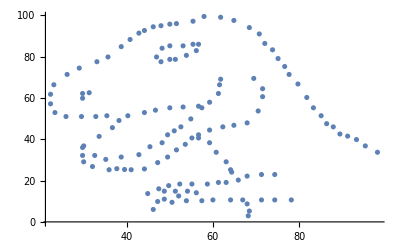

```mathematica
ListPlot[dataset]
```

Then, we will define a function to generate the descriptive statistics for this data.

```mathematica
summaryStatistics[data_]:={Mean[data],StandardDeviation[data],Correlation[data]⟦1,2⟧}
```

```mathematica
summaryStatistics[dataset]
```

{{54.2633,47.8323},{16.7651,26.9354},-0.0644719}

Now, we will select a shape that we want our dataset to conform to. In this notebook, we will proceed with a circle centered at {54.26,47.83}, with a radius of 30.

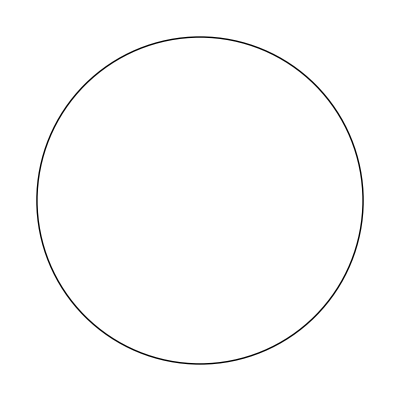

```mathematica
Graphics[Circle[{54.26,47.83},30]]
```

We will move individual coordinates by a small amount, in a random direction, chosen from a normal distribution.

The moveRandomPoint completes a single round of perturbation of the entire dataset, with {x,y} as each coordinate pair in the dataset.

```mathematica
moveRandomPoint[{x_,y_}]:={x,y}+RandomVariate[NormalDistribution[0,1],2];
```

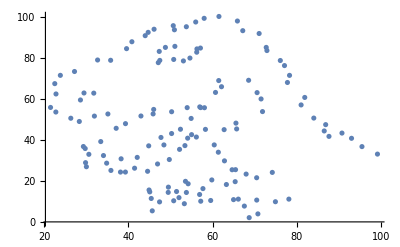

```mathematica
newDataset= Map[moveRandomPoint,dataset];
ListPlot[newDataset]
```

Once the individual points have been moved, we will use a fit function to check if the perturbed data better approximates the shape of choice, which in our example, is a circle.

To accomplish this task, let’s define a Fit function which computes the average distance between points in our dataset and our target shape, i.e. a circle.

```mathematica
functionFit1[{x_,y_}]:=List[RegionDistance[Circle[{54.26,47.83},30],{x,y}]];
functionFit[list_]:=Mean[Map[functionFit1,list]]
```

```mathematica
functionFit[newDataset]
```

{10.1672}

Right now, our algorithm implements the naive approach which accepts datasets with an improved fitness value. To mitigate the possibility of early convergence in locally-optimal solutions, Matejka et al. suggests a simulated annealing technique, which accepts solutions based on a “temperature” measure even if the fitness isn’t improved.

```mathematica
simulatedAnnealing[temp_:0.4]:=
initial = 0.4
RandomReal[]<temp
after each run, decrease using a cooling function until you reach 0.01
```

```mathematica
Range[RandomReal[],10]
```

{0.906102,1.9061,2.9061,3.9061,4.9061,5.9061,6.9061,7.9061,8.9061,9.9061}

The final step in our algorithm is to check whether the previous dataset and the new dataset is statistically equivalent, using an isErrorokay function.

```mathematica
isErrorokay[data1_,data2_]:=If[Abs[Total[Flatten[summaryStatistics[data1]-summaryStatistics[data2]]]]<1,True,False]
```

```mathematica
isErrorokay[dataset,newDataset]
```

True

Once the dataset has been perturbed sufficiently, we will check statistical equivalence using the summaryStatistics function we defined earlier. If they are equal (up to two decimal places), the dataset from the current iteration becomes the original dataset. If the distance between coordinates in our perturbed dataset is less than the corresponding coordinates in the original dataset, we will set the new data points. Then, we will repeat the process for a specified number of iterations.

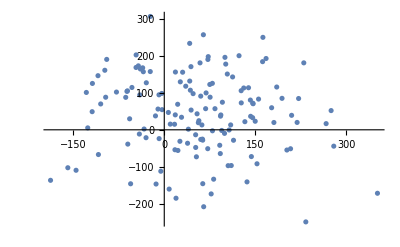

```mathematica
ListPlot[NestWhile[ Map[moveRandomPoint,#]&,dataset,functionFit[#]< functionFit[##] && isErrorokay[dataset,#]&,10000]]
```

```mathematica
Map[moveRandomPoint,dataset]
```

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a general case*)
```

## Implications

Though visually different, both the original dataset and the perturbed dataset display the same summary statistics. As a concluding remark, don’t trust the numbers until you’ve seen the shape of your data for yourself.

## Further explorations

Anscombe, F.J. (1973). Graphs in Statistical Analysis.
The American Statistician 27, 1, 17–21.

Matejka, J., & Fitzmaurice, G. (2017). Same Stats, Different Graphs: Generating Datasets with Varied Appearance and Identical Statistics Through Simulated Annealing. In Proceedings of the 2017 CHI Conference on Human Factors in Computing Systems (pp. 1290–1294). New York, NY, USA: ACM. https://doi.org/10.1145/3025453.3025912

Cairo, A. (n.d.). Download the Datasaurus: Never trust summary statistics alone; always visualize your data. Retrieved June 29, 2018, from http://www.thefunctionalart.com/2016/08/download-datasaurus-never-trust-summary.html

## Author contact information

tanha.kate@minerva.kgi.edu

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)